```mathematica
V[r_]=-1/r-(1.0415223038416566 ⅇ^(-0.9990999998788636 r))/r;α=2.;u0=1.*10^-8;r1=1500.;r2=u0;
```

```mathematica
sol=ParametricNDSolve[{u''[r]+(α(e-V[r])-0/r^2)u[r]==0,u[r1]==u0,u'[r1]==(*√(α(V[r1]-e)) u0*)-u0},
u,{r,r1,r2},e,Method->"Chasing",MaxSteps->Infinity,WorkingPrecision->20,MaxStepFraction->10^-3]
```

{u→ParametricFunction[<>]}

```mathematica
FindRoot[u[e][r2]==0/.sol,{e,-.0012,-.0013}]
```

{e→-0.0012937}

```mathematica
energy={};
```

```mathematica
AppendTo[energy,-e/.%]
```

{1.33732,0.186434,0.0710575,0.0374072,0.023051,0.0156184,0.00535929,0.0012937}

```mathematica
ene={};
ene=Flatten[Reap[Do[Sow[{i,energy[[i]]}],{i,1,6}];Sow[{10,energy[[7]]}];Sow[{20,energy[[8]]}]][[2]],1]
```

{{1,1.33732},{2,0.186434},{3,0.0710575},{4,0.0374072},{5,0.023051},{6,0.0156184},{10,0.00535929},{20,0.0012937}}

```mathematica
Solve[-1/(2 n^2)+c/(√π n^3)==-energy[[8]]/.n->20,c]
```

{{c→-0.619584}}

```mathematica
ϵ=Flatten[-Table[-1/(2 n^2)+c/(√π n^3)/.%50,{n,20}][[#]]&/@{1,2,3,4,5,6,10,20}](*the energy of perturbation*)
```

{0.849563,0.168695,0.0685023,0.0367119,0.0227965,0.0155072,0.00534956,0.0012937}

```mathematica
δϵ =Table[Abs[(ϵ[[i]]-energy[[i]])/energy[[i]]],{i,8}]
```

{0.574128,0.105152,0.0373,0.018938,0.0111627,0.00716794,0.00181884,0.}

```mathematica
Lδϵ={energy[[#]],δϵ[[#]]}&/@{1,2,3,4,5,6,7,8}
```

{{1.33732,0.574128},{0.186434,0.105152},{0.0710575,0.0373},{0.0374072,0.018938},{0.023051,0.0111627},{0.0156184,0.00716794},{0.00535929,0.00181884},{0.0012937,0.}}

```mathematica
LδE={energy[[#]],δE[[#]]}&/@{1,2,3,4,5,6,7,8}
(*AppendTo[LδE,{N[1/10^2],δE[[7]]}]
AppendTo[LδE,{N[1/20^2],δE[[8]]}]*)
```

{{1.33732,0.33732},{0.186434,0.254264},{0.0710575,0.360483},{0.0374072,0.401485},{0.023051,0.423726},{0.0156184,0.437738},{0.00535929,0.737395},{0.0012937,0.917203}}

```mathematica
δE=Table[Abs[(1/i^2-energy[[i]])/energy[[i]]],{i,8}]
```

{0.33732,0.254264,0.360483,0.401485,0.423726,0.437738,0.737395,0.917203}

```mathematica
LδE
Lδϵ
```

{{1.33732,0.33732},{0.186434,0.254264},{0.0710575,0.360483},{0.0374072,0.401485},{0.023051,0.423726},{0.0156184,0.437738},{0.00535929,0.737395},{0.0012937,0.917203}}

{{1.33732,0.574128},{0.186434,0.105152},{0.0710575,0.0373},{0.0374072,0.018938},{0.023051,0.0111627},{0.0156184,0.00716794},{0.00535929,0.00181884},{0.0012937,0.}}

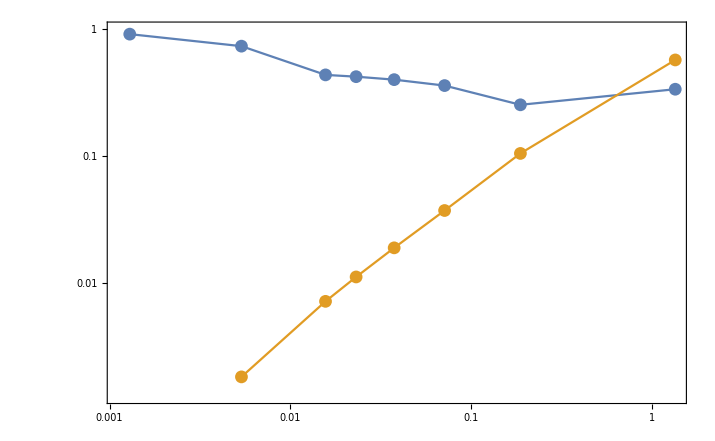

```mathematica
Show[ListLogLogPlot[{LδE,Lδϵ},Joined->True],ListLogLogPlot[{LδE,Lδϵ}],Frame->True]
```

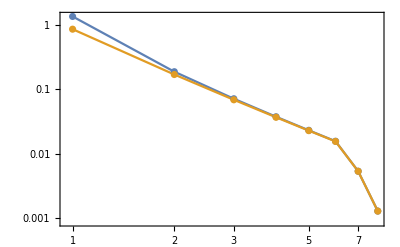

```mathematica
Show[ListLogLogPlot[{energy,ϵ},Joined->True,Frame->True],ListLogLogPlot[{energy,ϵ}]]
```

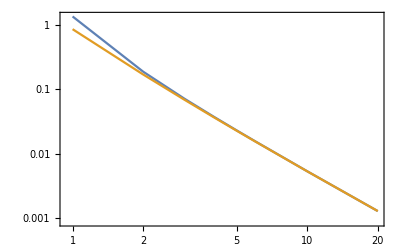

```mathematica
ListLogLogPlot[{Join[Partition[{1,2,3,4,5,6,10,20},1],Partition[energy,1],2],Join[Partition[{1,2,3,4,5,6,10,20},1],Partition[ϵ,1],2]},Joined->True,Frame->True]
```

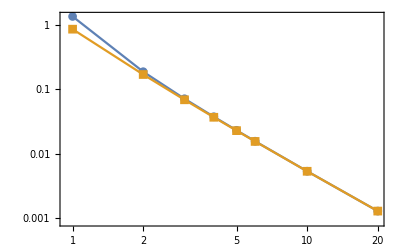

```mathematica
ListLogLogPlot[{#1,#2},Joined->True,Frame->True,PlotMarkers->Automatic]&[Join[Partition[{1,2,3,4,5,6,10,20},1],Partition[energy,1],2],Join[Partition[{1,2,3,4,5,6,10,20},1],Partition[ϵ,1],2]]
```